```mathematica
F[x_]:=Module[{m=0,c={}},
For[i=1,i≤x,i++,
a=Length[Divisors[i]];
If[a>m,m=a;AppendTo[c,i]];];
Return[c]]
```

```mathematica
F[100000]
```

{1,2,4,6,12,24,36,48,60,120,180,240,360,720,840,1260,1680,2520,5040,7560,10080,15120,20160,25200,27720,45360,50400,55440,83160}

```mathematica
FactorInteger[%]
```

{{{1,1}},{{2,1}},{{2,2}},{{2,1},{3,1}},{{2,2},{3,1}},{{2,3},{3,1}},{{2,2},{3,2}},{{2,4},{3,1}},{{2,2},{3,1},{5,1}},{{2,3},{3,1},{5,1}},{{2,2},{3,2},{5,1}},{{2,4},{3,1},{5,1}},{{2,3},{3,2},{5,1}},{{2,4},{3,2},{5,1}},{{2,3},{3,1},{5,1},{7,1}},{{2,2},{3,2},{5,1},{7,1}},{{2,4},{3,1},{5,1},{7,1}},{{2,3},{3,2},{5,1},{7,1}},{{2,4},{3,2},{5,1},{7,1}},{{2,3},{3,3},{5,1},{7,1}},{{2,5},{3,2},{5,1},{7,1}},{{2,4},{3,3},{5,1},{7,1}},{{2,6},{3,2},{5,1},{7,1}},{{2,4},{3,2},{5,2},{7,1}},{{2,3},{3,2},{5,1},{7,1},{11,1}},{{2,4},{3,4},{5,1},{7,1}},{{2,5},{3,2},{5,2},{7,1}},{{2,4},{3,2},{5,1},{7,1},{11,1}},{{2,3},{3,3},{5,1},{7,1},{11,1}}}

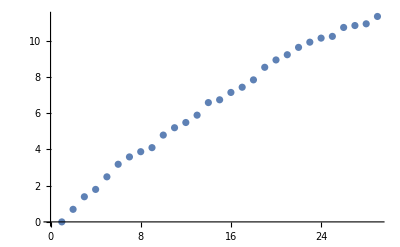

```mathematica
ListPlot[Log[%9]]
```

```mathematica
FactorInteger[83160]
```

{{2,3},{3,3},{5,1},{7,1},{11,1}}

```mathematica
Table[Fibonacci[x],{x,1,10}]
```

{1,1,2,3,5,8,13,21,34,55}

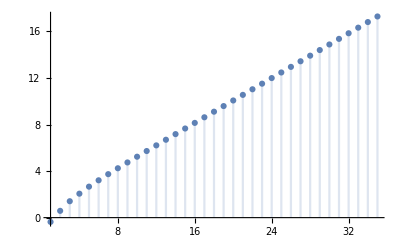

```mathematica
DiscretePlot[{Log[Log[Times@@(Prime[Range[y]]^Reverse[Fibonacci[Range[y]]])]]},{y,1,35}]
```

```mathematica
Times@@{23,29}
```

667

```mathematica
Tiems
```

```mathematica
Reverse[Fibonacci[Range[10]]]
```

{55,34,21,13,8,5,3,2,1,1}

```mathematica
{1,2}^{3,4}
```

{1,16}